```mathematica
Integrate[Sin[x]^2,x]
```

x/2-1/4 Sin[2 x]

```mathematica
NIntegrate[x*Exp[x]*Sin[x],{x,0,1}]
```

0.643678

```mathematica
ContourPlot3D[{z==5(x^2+y^2),z==6-7 x^2-y^2},{x,-5,5},{y,-5,5},{z,12,6},Axes->True,Boxed->False]
```

```mathematica
(-Graphics3D-)^□
```

```mathematica
f[x_,y_]=5(x^2+y^2);
g[x_,y_]=6-7 x^2-y^2;
s1=Solve[f[x,y]==g[x,y],y]
```

{{y→-√(1-2 x^2)},{y→√(1-2 x^2)}}

```mathematica
s2=Solve[s1[[1,1,2]]==0,x]
```

{{x→-1/(√2)},{x→1/(√2)}}

```mathematica
∫_(-1/√2)^(1/√2) ∫_(-√(1-2 x^2))^(√(1-2 x^2)) ∫_f[x,y]^g[x,y] 1ⅆzⅆyⅆx//N
```

6.66432

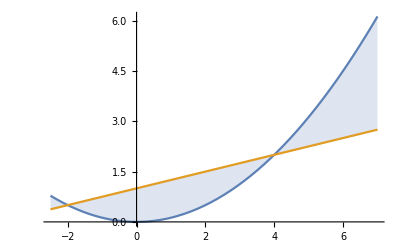

```mathematica
f[y_]=y^2/8;
g[y_]=(y+4)/4;
Plot[{f[y],g[y]},{y,-2.5,7},Filling->{1->{2}}]
```

```mathematica
NSolve[f[y]==g[y]]
```

{{y→-2.},{y→4.}}

```mathematica
Integrate[-f[y]+g[y],{y,-3.58258,5.58258}]
```

2.29127